23

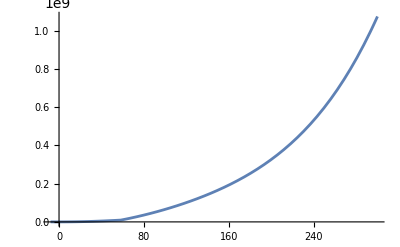

```mathematica
v0 := 246.22
mW:=80.3692
mZ:=91.1880
mh := 125.20
mH :=56
mA:=471
mHpm:=471
l345:=0.0037
g:=2*mW/v0
gY:=Sqrt[4*mZ^2/v0^2-g^2]
mt:=172.56
yt:=Sqrt[2.0]*mt/v0

Q:=v0 (*Renormalisation scale*)
eps:=10^(-10)

lam1:= 0.5*mh^2/v0^2
lam2:= 0.4
lam3:=(l345+2*(mHpm^2-mH^2)/v0^2)
lam4:=(mA^2+mH^2-2*mHpm^2)/v0^2
lam5:=(mH^2-mA^2)/v0^2
msq1:=-lam1*v0^2
msq2:=(mHpm^2-lam3*v0^2/2)

(*Gauge boson masses*)
msqW[x_,y_]:=g^2*(x^2+y^2)/4
msqZ[x_,y_]:=(g^2+gY^2)*(x^2+y^2)/4
msqW0T:=g^2*v0^2/4
msqZ0T:=(g^2+gY^2)*v0^2/4

(*Top quark mass*)
msqt[x_,y_]:=x^2*yt^2/2
msqt0T:=mt^2

(*Scalar masses, sign-swap: Sign[(massS00[x,y]-massS11[x,y])]*)
massS00[x_,y_]:=msq1+3*lam1*x^2+l345*y^2/2
massS11[x_,y_]:=msq2+l345*x^2/2+3*lam2*y^2
massS01[x_,y_]:=l345*x*y
DetS[x_,y_]:=(massS00[x,y]-massS11[x,y])^2+4*massS01[x,y]^2
msqS1[x_,y_]:=0.5*(massS00[x,y]+massS11[x,y]+1*Sqrt[DetS[x,y]])
msqS2[x_,y_]:=0.5*(massS00[x,y]+massS11[x,y]-1*Sqrt[DetS[x,y]])

(*Pseudo scalar masses, sign-swap: Sign[(massP00[x,y]-massP11[x,y])]*)
massP00[x_,y_]:=msq1+lam1*x^2+(l345-2*lam5)*y^2/2
massP11[x_,y_]:=msq2+(l345-2*lam5)*x^2/2+lam2*y^2
massP01[x_,y_]:=lam5*x*y
DetP[x_,y_]:=massP00[x,y]^2-2*massP00[x,y]*massP11[x,y]+massP11[x,y]^2+4*massP01[x,y]^2
XP[x_,y_]:=If[-massP00[x,y]+massP11[x,y]+Sqrt[DetP[x,y]]-2*massP01[x,y]>=0,1,-1]
msqP1[x_,y_]:=0.5*(massP00[x,y]+massP11[x,y]-1*Sqrt[DetP[x,y]])
msqP2[x_,y_]:=0.5*(massP00[x,y]+massP11[x,y]+1*Sqrt[DetP[x,y]])

(*Charged scalar masses, sign-swap: Sign[(masspm00[x,y]-masspm11[x,y])]*)
masspm00[x_,y_]:=msq1+lam1*x^2+lam3*y^2/2
masspm11[x_,y_]:=msq2+lam3*x^2/2+lam2*y^2
masspm01[x_,y_]:=(lam4+lam5)*x*y/2
Detpm[x_,y_]:=(masspm00[x,y]-masspm11[x,y])^2+4*masspm01[x,y]^2
msqpm1[x_,y_]:=0.5*(masspm00[x,y]+masspm11[x,y]-1*Sqrt[Detpm[x,y]])
msqpm2[x_,y_]:=0.5*(masspm00[x,y]+masspm11[x,y]+1*Sqrt[Detpm[x,y]])

(*Thermally corrected masses*)
piPhi[T_]:=T^2/24*(6*yt^2+(9/2)*g^2+(3/2)*gY^ 2+12*lam1+4*lam3+2*lam4)
piEta[T_]:=T^2/24*((9/2)*g^2+(3/2)*gY^2+12*lam2+4*lam3+2*lam4)

(*Gauge bosons have tranversal and longitudinal components
Longitudinal components have relevant daisy contributions
So we should introduce thermally corrected masses for longitudinal modes.*)
msqWL[x_,y_,T_]:=g^2*(x^2+y^2)/4+2*g^2*T^2

(*The photon also gets a thermal correction
Finding this mass one should diagonalise the mass matrix*)
piB[T_]:=2*gY^2*T^2
piW[T_]:=2*g^2*T^2
m1sq[x_,y_]:=gY^2*(x^2+y^2)/4
m2sq[x_,y_]:=g^2*(x^2+y^2)/4
m12sq[x_,y_]:=-gY*g*(x^2+y^2)/4

msqEig1[x_,y_,T_]:=(m1sq[x,y]+m2sq[x,y]+piB[T]+piW[T]
-Sqrt[4*m12sq[x,y]^2+(m2sq[x,y]-m1sq[x,y]-piB[T]+piW[T])^2])/2

msqEig2[x_,y_,T_]:=(m1sq[x,y]+m2sq[x,y]+piB[T]+piW[T]
+Sqrt[4*m12sq[x,y]^2+(m2sq[x,y]-m1sq[x,y]-piB[T]+piW[T])^2])/2

(*Scalar masses thermally corrected*)
massS00T[x_,y_,T_]:=massS00[x,y]+piPhi[T]
massS11T[x_,y_,T_]:=massS11[x,y]+piEta[T]
DetST[x_,y_,T_]:=(massS00T[x,y,T]-massS11T[x,y,T])^2+4*massS01[x,y]^2
msqS1T[x_,y_,T_]:=0.5*(massS00T[x,y,T]+massS11T[x,y,T]+Sqrt[DetST[x,y,T]])
msqS2T[x_,y_,T_]:=0.5*(massS00T[x,y,T]+massS11T[x,y,T]-Sqrt[DetST[x,y,T]])

(*Pseudo scalar masses thermally corrected*)
massP00T[x_,y_,T_]:=massP00[x,y]+piPhi[T]
massP11T[x_,y_,T_]:=massP11[x,y]+piEta[T]
DetPT[x_,y_,T_]:=(massP00T[x,y,T]-massP11T[x,y,T])^2+4*massP01[x,y]^2
msqP1T[x_,y_,T_]:=0.5*(massP00T[x,y,T]+massP11T[x,y,T]-Sqrt[DetPT[x,y,T]])
msqP2T[x_,y_,T_]:=0.5*(massP00T[x,y,T]+massP11T[x,y,T]+Sqrt[DetPT[x,y,T]])

(*Charged scalar masses, thermally corrected*)
masspm00T[x_,y_,T_]:=masspm00[x,y]+piPhi[T]
masspm11T[x_,y_,T_]:=masspm11[x,y]+piEta[T]
DetpmT[x_,y_,T_]:=(masspm00T[x,y,T]-masspm11T[x,y,T])^2+4*masspm01[x,y]^2
msqpm1T[x_,y_,T_]:=0.5*(masspm00T[x,y,T]+masspm11T[x,y,T]-Sqrt[DetpmT[x,y,T]])
msqpm2T[x_,y_,T_]:=0.5*(masspm00T[x,y,T]+masspm11T[x,y,T]+Sqrt[DetpmT[x,y,T]])

(*The thermal functions are defined as follows*)
JfNum[x_?NumericQ]:=-NIntegrate[t^2*Log[1+Exp[-Sqrt[t^2+x]]],{t,0,Infinity}]
JbNum[x_?NumericQ]:=NIntegrate[t^2*Log[1-Exp[-Sqrt[t^2+x]]], {t,0,Infinity}]
(*Plot[JfNum[x],{x,0,150}]*)

(*Tree-level potential*)
V0[x_,y_]:=msq1*x^2/2+msq2*y^2/2+lam1*x^4/4+lam2*y^4/4+l345*x^2*y^2/4
(*Coleman-Weinberg potential, Field-dependent masses*)
VCW[x_,y_]:=1/(64*Pi^2)*(4*msqW[x,y]^2*(Log[Abs[msqW[x,y]+eps]/Q^2]-1/2)(*Transverse W-bosons Ci=5/6(this is wrong) (or Ci=1/2(this is right))*)
+2*msqW[x,y]^2*(Log[Abs[msqW[x,y]+eps]/Q^2]-3/2)(*Longitudinal W-bosons Ci=3/2*)
+2*msqZ[x,y]^2*(Log[Abs[msqZ[x,y]+eps]/Q^2]-1/2)(*Transverse B-boson Ci=5/6(this is wrong) (or Ci=1/2(this is right))*)
+msqZ[x,y]^2*(Log[Abs[msqZ[x,y]+eps]/Q^2]-3/2)(*Longitudinal B-boson Ci=3/2*)
+msqS1[x,y]^2*(Log[Abs[msqS1[x,y]]/Q^2]-3/2)
+msqS2[x,y]^2*(Log[Abs[msqS2[x,y]]/Q^2]-3/2)
+msqP1[x,y]^2*(Log[Abs[msqP1[x,y]]/Q^2]-3/2)
+msqP2[x,y]^2*(Log[Abs[msqP2[x,y]]/Q^2]-3/2)
+2*msqpm1[x,y]^2*(Log[Abs[msqpm1[x,y]]/Q^2]-3/2)
+2*msqpm2[x,y]^2*(Log[Abs[msqpm2[x,y]]/Q^2]-3/2)
-12*msqt[x,y]^2*(Log[Abs[msqt[x,y]+eps]/Q^2]-3/2))


(*Coleman-Weinberg potential, thermally corrected masses*)
VCWT[x_,y_,T_]:=1/(64*Pi^2)*(4*msqW[x,y]^2*(Log[Abs[msqW[x,y]+eps]/Q^2]-1/2) (*Transverse W bosons*)
+2*msqWL[x,y,T]^2*(Log[Abs[msqWL[x,y,T]+eps]/Q^2]-3/2)(*Longitudinal W bosons*)
+2*msqZ[x,y]^2*(Log[Abs[msqZ[x,y]+eps]/Q^2]-1/2)(*Transverse Z boson*)
+msqEig1[x,y,T]^2*(Log[Abs[msqEig1[x,y,T]]/Q^2])(*Longitudinal photon*)
+msqEig2[x,y,T]^2*(Log[Abs[msqEig2[x,y,T]]/Q^2]-3/2)(*Longitudinal Z boson*)
+msqS1T[x,y,T]^2*(Log[Abs[msqS1T[x,y,T]]/Q^2]-3/2)
+msqS2T[x,y,T]^2*(Log[Abs[msqS2T[x,y,T]]/Q^2]-3/2)
+msqP1T[x,y,T]^2*(Log[Abs[msqP1T[x,y,T]]/Q^2]-3/2)
+msqP2T[x,y,T]^2*(Log[Abs[msqP2T[x,y,T]]/Q^2]-3/2)
+2*msqpm1T[x,y,T]^2*(Log[Abs[msqpm1T[x,y,T]]/Q^2]-3/2)
+2*msqpm2T[x,y,T]^2*(Log[Abs[msqpm2T[x,y,T]]/Q^2]-3/2)
-12*msqt[x,y]^2*(Log[Abs[msqt[x,y]+eps]/Q^2]-3/2))

(*Renormalised Coleman-Weinberg potential*)
VCWR[x_,y_]:=1/(64*Pi^2)*(6*(msqW[x,y]^2*(Log[Abs[msqW[x,y]+eps]/msqW0T]-3/2) +2*msqW0T*msqW[x,y])
+3*(msqZ[x,y]^2*(Log[Abs[msqZ[x,y]+eps]/msqZ0T]-3/2)+2*msqZ0T*msqZ[x,y])
+msqS1[x,y]^2*(Log[Abs[msqS1[x,y]]/mh^2]-3/2)+2*mh^2*msqS1[x,y]
+msqS2[x,y]^2*(Log[Abs[msqS2[x,y]]/mH^2]-3/2)+2*mH^2*msqS2[x,y]
+msqP1[x,y]^2*(Log[Abs[msqP1[x,y]]/mh^2]-3/2)
+msqP2[x,y]^2*(Log[Abs[msqP2[x,y]]/mA^2]-3/2)+2*mA^2*msqP2[x,y]
+2*msqpm1[x,y]^2*(Log[Abs[msqpm1[x,y]]/mh^2]-3/2)
+2*(msqpm2[x,y]^2*(Log[Abs[msqpm2[x,y]]/mHpm^2]-3/2)+2*mHpm^2*msqpm2[x,y])
-12*(msqt[x,y]^2*(Log[Abs[msqt[x,y]+eps]/mt^2]-3/2)+2*mt^2*msqt[x,y])
)

(*Renormalised Coleman-Weinberg potential, using Cline and Lemieux Goldstone treatment*)
VCWRCL[x_,y_]:=1/(64*Pi^2)*(6*(msqW[x,y]^2*(Log[Abs[msqW[x,y]+eps]/msqW0T]-3/2) +2*msqW0T*msqW[x,y])
+3*(msqZ[x,y]^2*(Log[Abs[msqZ[x,y]+eps]/msqZ0T]-3/2)+2*msqZ0T*msqZ[x,y])
+msqS1[x,y]^2*(Log[Abs[msqS1[x,y]]/mh^2]-3/2)+2*mh^2*msqS1[x,y]
+msqS2[x,y]^2*(Log[Abs[msqS2[x,y]]/mH^2]-3/2)+2*mH^2*msqS2[x,y]
+msqP1[x,y]^2*(Log[Abs[msqP1[x,y]]/mh^2]+1/2)
+msqP2[x,y]^2*(Log[Abs[msqP2[x,y]]/mA^2]-3/2)+2*mA^2*msqP2[x,y]
+2*msqpm1[x,y]^2*(Log[Abs[msqpm1[x,y]]/mh^2]+1/2)
+2*(msqpm2[x,y]^2*(Log[Abs[msqpm2[x,y]]/mHpm^2]-3/2)+2*mHpm^2*msqpm2[x,y])
-12*(msqt[x,y]^2*(Log[Abs[msqt[x,y]+eps]/mt^2]-3/2)+2*mt^2*msqt[x,y])
)

(*Renormalised Coleman-Weinberg potential with thermally corrected masses*)
VCWRT[x_,y_,T_]:=1/(64*Pi^2)*(4*(msqW[x,y]^2*(Log[Abs[msqW[x,y]+eps]/msqW0T]-3/2) +2*msqW0T*msqW[x,y]) (*Tranversal W-boson modes*)
+2*(msqWL[x,y,T]^2*(Log[Abs[msqWL[x,y,T]+eps]/msqW0T]-3/2)+2*msqW0T*msqWL[x,y,T]) (*Longitudinal W-boson modes*)
+2*(msqZ[x,y]^2*(Log[Abs[msqZ[x,y]+eps]/msqZ0T]-3/2)+2*msqZ0T*msqZ[x,y])   (*Tranversal Z-boson modes*)
(*+msqEig1[x,y,T]^2*(Log[Abs[msqEig1[x,y,T]+eps]/0]-3/2)    HELP! The photon mass vanishes at zero-temperature!*)
+msqEig2[x,y,T]^2*(Log[Abs[msqEig2[x,y,T]+eps]/msqZ0T]-3/2) +2*msqZ0T*msqEig2[x,y,T] (*Longitudinal Z-boson*)
+msqS1T[x,y,T]^2*(Log[Abs[msqS1T[x,y,T]]/mh^2]-3/2)+2*mh^2*msqS1T[x,y,T]
+msqS2T[x,y,T]^2*(Log[Abs[msqS2T[x,y,T]]/mH^2]-3/2)+2*mH^2*msqS2T[x,y,T]
+msqP1T[x,y,T]^2*(Log[Abs[msqP1T[x,y,T]]/mh^2]-3/2)
+msqP2T[x,y,T]^2*(Log[Abs[msqP2T[x,y,T]]/mA^2]-3/2)+2*mA^2*msqP2T[x,y,T]
+2*msqpm1T[x,y,T]^2*(Log[Abs[msqpm1T[x,y,T]]/mh^2]-3/2)
+2*(msqpm2T[x,y,T]^2*(Log[Abs[msqpm2T[x,y,T]]/mHpm^2]-3/2)+2*mHpm^2*msqpm2T[x,y,T])
-12*(msqt[x,y]^2*(Log[Abs[msqt[x,y]+eps]/mt^2]-3/2)+2*mt^2*msqt[x,y])
)

(*Derivatives of VCW to h and H at electroweak vacuum*)
DVCWh[x_,y_,T_]:=Derivative[1,0,0][VCWT[x,y,T]]
DVCWhh[x_,y_,T_]:=Derivative[2,0,0][VWCT[x,y,T]]
DVCWHH[x_,y_,T_]:=Derivative[0,2,0][VCWT[x,y,T]]

(*Counterterms coefficients calculated explicitly*)
dmh:=(1/2)*DVCWhh[v0,0,0]-(3/(2*v0))*DVCWh[v0,0,0](*Mathematica does not work like this, write down all terms:}(  *)
dmH:=-DVCWHH[v0,0,0]
dlam1:=(1/(2*v0^2))*((1/v0)*DVCWh[v0,0,0]-DVCWhh[v0,0,0])
VCTex[x_,y_]:=dmh*x^2/2+dmH*y^2/2+dlam1*x^4/4

(*Counterterms from renormalised Coleman-Weinberg potential*)
VCT[x_,y_]:=-1/(64*Pi^2)*(4*(msqW[x,y]^2*(Log[msqW0T/Q^2]+1)-2*msqW0T*msqW[x,y])(*Transverse W bosons*)
+2*(msqW[x,y]^2*(Log[msqW0T/Q^2]) -2*msqW0T*msqW[x,y])(*Longitudinal W bosons*)
+2*(msqZ[x,y]^2*(Log[msqZ0T/Q^2]+1)-2*msqZ0T*msqZ[x,y])(*Transverse Z boson*)
+msqZ[x,y]^2*(Log[msqZ0T/Q^2])-2*msqZ0T*msqZ[x,y](*Longitudinal Z boson*)
+msqS1[x,y]^2*Log[mh^2/Q^2]-2*mh^2*msqS1[x,y]
+msqS2[x,y]^2*Log[mH^2/Q^2]-2*mH^2*msqS2[x,y]
+msqP1[x,y]^2*Log[mh^2/Q^2]
+msqP2[x,y]^2*Log[mA^2/Q^2]-2*mA^2*msqP2[x,y]
+2*msqpm1[x,y]^2*Log[mh^2/Q^2]
+2*(msqpm2[x,y]^2*Log[mHpm^2/Q^2]-2*mHpm^2*msqpm2[x,y])
-12*(msqt[x,y]^2*Log[mt^2/Q^2]-2*mt^2*msqt[x,y])
)

(*Thermal potential*)
VT[x_,y_,T_]:=T^4/(2*Pi^2)*(2*JbNum[Abs[msqWL[x,y,T]]/T^2](*longitudinal W*)
+4*JbNum[Abs[msqW[x,y]]/T^2](*Transverse W*)
+2*JbNum[Abs[msqZ[x,y]]/T^2](*transverse Z*)
+JbNum[Abs[msqEig2[x,y,T]]/T^2](*Longitudinal Z*)
+JbNum[Abs[msqEig1[x,y,T]]/T^2](*Photon*)
+JbNum[Abs[msqS1T[x,y,T]]/T^2]
+JbNum[Abs[msqS2T[x,y,T]]/T^2]
+JbNum[Abs[msqP1T[x,y,T]]/T^2]
+JbNum[Abs[msqP2T[x,y,T]]/T^2]
+2*JbNum[Abs[msqpm1T[x,y,T]]/T^2]
+2*JbNum[Abs[msqpm2T[x,y,T]]/T^2]
+12*JfNum[Abs[msqt[x,y]]/T^2]            (*top quark "-" already in definition of Jf*)
)


(*Effective potential, all different configurations are possible
The thermally corrected masses can be introduced in the CW-potential
the thermal potential and in the combination of CW and counterterms.*)
Veff[x_,y_,T_]:=V0[x,y]+VCWR[x,y]+VT[x,y,T](*+VCT[x,y]*)
VeffCL[x_,y_,T_]:=V0[x,y]+VCWRCL[x,y]+VT[x,y,T]
(*Remove this before submitting*)(*
V0[50.,0]
VCWRT[50.,0,100]
VT[50.,0,100]
*)
(*The temperature can be inserted here manually*)
T=23

(*Eigenvalues of mass matrices plotted, next to the diagonal components, with only H or mixed h and H field values*)
(*Plot[{(*msqS1[0,x],msqS2[0,x],*)Sqrt[msqW[x,0]],Sqrt[Abs[massP00[x,0]]],Sqrt[Abs[massP11[x,0]]],Sqrt[Abs[msqP1[x,0]]],(*msqP1[0.00000001*x,x],*)Sqrt[Abs[msqP2[x,0]]](*,msqpm1[x,6*x],msqpm2[x,6*x]*)(*msqP1T[0,x,T],msqP2T[0,x,T]*)},{x,0,250}, PlotRange->All,AxesLabel->{H ,M^2},PlotStyle->{Red,Blue,Cyan,Yellow}]*)
(*The determinants, with the seperate terms from the determinants*)
(*Plot[{DetP[0.1*x/Sqrt[1.01],x/Sqrt[1.01]],(*(massP00[0.1*x,x]-massP11[0.1*x,x])^2*),DetP[0,x](*,4*massP01[0.1*x,x]^2*)},{x,30,60}]*)
(*Effective potential*)
(*Plot[{Veff[0,x,69.4]-Veff[0,0,69.4],Veff[0,x,T]-Veff[0,0,T]},{x,-120,120}, PlotRange ->All(*{{-190,190},{-1000000,3000000}}*)
]*)
Plot[{Veff[0,x,T]-Veff[0,0,T]},{x,-8,300}, PlotRange -> All]
(*Contourplot effective potential*)
(*ContourPlot[Veff[x,y,69.4],{x,0,250},{y,0,150},Contours->30,ContourShading->None,FrameLabel->{"h","H"}]*)
(*Animation of mass eigenvalues and diagonal components, starting at H-axis slowly tilting the trajectory to angle 6 deg.*)
(*Anim=Table[Plot[{massP00[t*x,x],massP11[t*x,x],msqP1[t*x,x],msqP2[t*x,x]},{x,30,80}, AxesLabel->{x,M^2},PlotStyle->{Red,Blue,Cyan,Yellow},PlotRange->{{30,80},{-5000,20000}},ImageSize->500,PlotLegends->TextString@Row@{"T=",t}],{t,0.001,0.1,.002}];
Export["eigenvalues.gif",Anim]*)
```

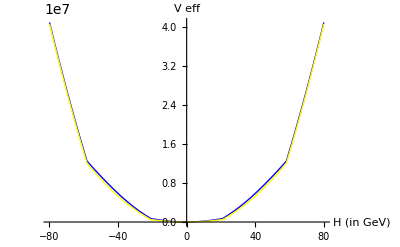

```mathematica
Show[%1377,AxesLabel->{HoldForm[H (in GeV)],HoldForm[V eff]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]}]
```

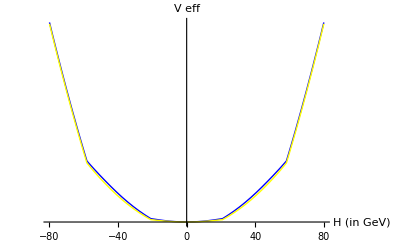

```mathematica
Show[%1378,Ticks->{Automatic,None},Method->{"DefaultBoundaryStyle"->Automatic,"DefaultGraphicsInteraction"->{"Version"->1.2,"TrackMousePosition"->{True,False},"Effects"->{"Highlight"->{"ratio"->2},"HighlightPoint"->{"ratio"->2},"Droplines"->{"freeformCursorMode"->True,"placement"->{"x"->"All","y"->"None"}}}},"DefaultMeshStyle"->AbsolutePointSize[6],"ScalingFunctions"->None,"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}}]
```

```mathematica
Export["G:\\My Drive\\Documenten\\natomap\\Master Project\\Images\\Veff_CL.png",%1379,"PNG"]
```

G:\My Drive\Documenten\natomap\Master Project\Images\Veff_CL.png

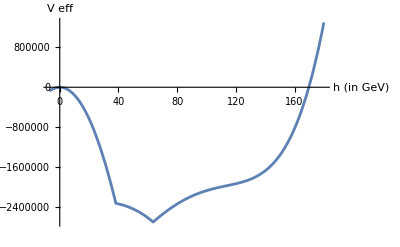

```mathematica
Show[%182,AxesLabel->{HoldForm[h (in GeV)],HoldForm[V eff]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]}]
```

```mathematica
Export["G:\\My Drive\\Documenten\\natomap\\Master Project\\Images\\benin_1StepCW_T119_37.png",%183,"PNG"]
```

G:\My Drive\Documenten\natomap\Master Project\Images\benin_1StepCW_T119_37.png

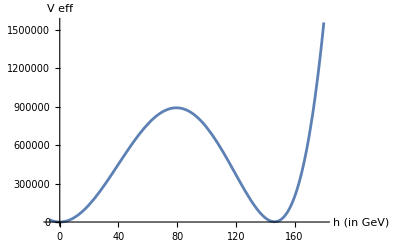

```mathematica
Show[%90,AxesLabel->{HoldForm[h (in GeV)],HoldForm[V eff]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]}]
```

```mathematica
Export["G:\\My Drive\\Documenten\\natomap\\Master Project\\Images\\benin_1StepCWCT_T119_37.png",%91,"PNG"]
```

G:\My Drive\Documenten\natomap\Master Project\Images\benin_1StepCWCT_T119_37.png

```mathematica
Show[%634,AxesLabel->{HoldForm[h (in GeV)],HoldForm[V eff]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]}]
```

-Graphics-

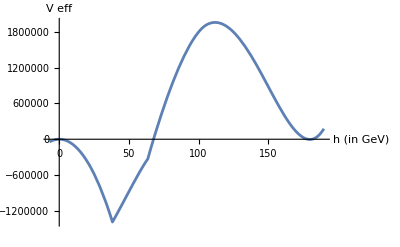

```mathematica
Show[%452,AxesLabel->{HoldForm[h (in GeV)],HoldForm[V eff]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]}]
```

```mathematica
Export["G:\\My Drive\\Documenten\\natomap\\Master Project\\Images\\Benin_1StepVT_T_106_42.png",%453,"PNG"]
```

G:\My Drive\Documenten\natomap\Master Project\Images\Benin_1StepVT_T_106_42.png

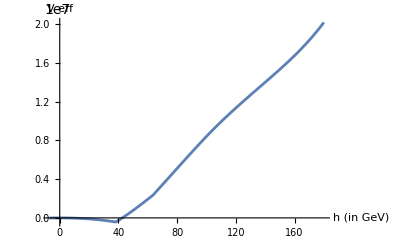

```mathematica
Show[%90,AxesLabel->{HoldForm[h (in GeV)],HoldForm[V eff]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]}]
```

```mathematica
Export["G:\\My Drive\\Documenten\\natomap\\Master Project\\Images\\Benin_1StepVT_T_119_37.png",%91,"PNG"]
```

G:\My Drive\Documenten\natomap\Master Project\Images\Benin_1StepVT_T_119_37.png

```mathematica
Show[%810,AxesLabel->{HoldForm[h (in GeV)],HoldForm[V eff]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]}]
```

-Graphics-

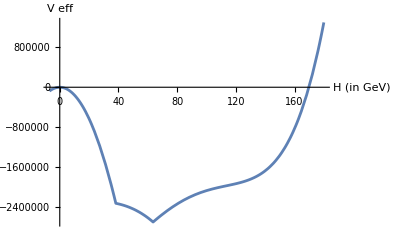

```mathematica
Show[%362,AxesLabel->{HoldForm[H (in GeV)],HoldForm[V eff]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]}]
```

```mathematica
Export["G:\\My Drive\\Documenten\\natomap\\Master Project\\Images\\benin_1StepCW_T119_37.png",%363,"PNG"]
```

G:\My Drive\Documenten\natomap\Master Project\Images\benin_1StepCW_T119_37.png

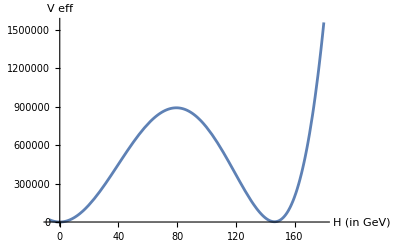

```mathematica
Show[%270,AxesLabel->{HoldForm[H (in GeV)],HoldForm[V eff]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]}]
```

```mathematica
Export["G:\\My Drive\\Documenten\\natomap\\Master Project\\Images\\benin_1StepCWCT_T119_37.png",%271,"PNG"]
```

G:\My Drive\Documenten\natomap\Master Project\Images\benin_1StepCWCT_T119_37.png

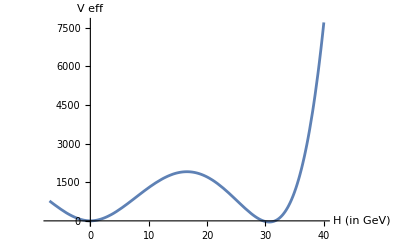

```mathematica
Show[%90,AxesLabel->{HoldForm[H (in GeV)],HoldForm[V eff]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]}]
```

```mathematica
Export["G:\\My Drive\\Documenten\\natomap\\Master Project\\Images\\benin_2StepCW_T147_964.png",%91,"PNG"]
```

G:\My Drive\Documenten\natomap\Master Project\Images\benin_2StepCW_T147_964.png

```mathematica
Show[%1172,AxesLabel->{HoldForm[H (in GeV)],HoldForm[V eff]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]}]
```

-Graphics-

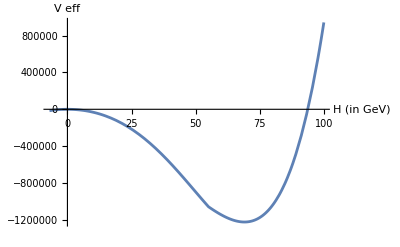

```mathematica
Show[%90,AxesLabel->{HoldForm[H (in GeV)],HoldForm[V eff]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]}]
```

```mathematica
Export["G:\\My Drive\\Documenten\\natomap\\Master Project\\Images\\Benin_2StepCW.png",%91,"PNG"]
```

G:\My Drive\Documenten\natomap\Master Project\Images\Benin_2StepCW.png

```mathematica
in
```

```mathematica
Show[%2687,AxesLabel->{HoldForm[H (in GeV)],HoldForm[V eff]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]}]
```

-Graphics-

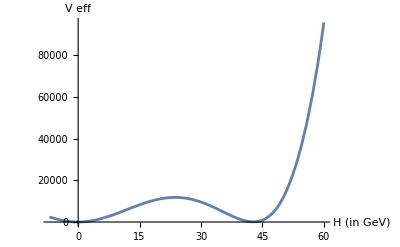

```mathematica
Show[%2415,AxesLabel->{HoldForm[H (in GeV)],HoldForm[V eff]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]}]
```

```mathematica
Export["G:\\My Drive\\Documenten\\natomap\\Master Project\\Images\\Benin_2StepCWCT.png",%2416,"PNG"]
```

G:\My Drive\Documenten\natomap\Master Project\Images\Benin_2StepCWCT.png

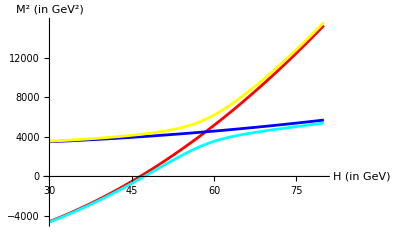

```mathematica
Show[%88,AxesLabel->{HoldForm[HoldForm[H] (in GeV)],HoldForm[HoldForm[M^2] (in GeV^2)]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]}]
```

```mathematica
Export["G:\\My Drive\\Documenten\\natomap\\Master Project\\Images\\eigenvalues_middenveld.png",%89,"PNG"]
```

G:\My Drive\Documenten\natomap\Master Project\Images\eigenvalues_middenveld.png

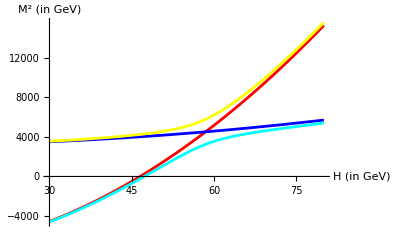

```mathematica
Show[%1408,AxesLabel->{HoldForm[HoldForm[H] (in GeV)],HoldForm[HoldForm[M^2] (in GeV)]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]}]
```

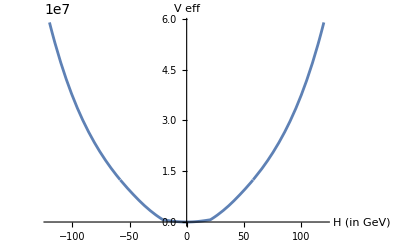

```mathematica
Show[%88,AxesLabel->{HoldForm[H (in GeV)],HoldForm[V eff]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]}]
```

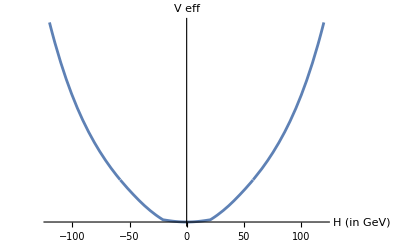

```mathematica
Show[%89,Ticks->{Automatic,None},Method->{"DefaultBoundaryStyle"->Automatic,"DefaultGraphicsInteraction"->{"Version"->1.2,"TrackMousePosition"->{True,False},"Effects"->{"Highlight"->{"ratio"->2},"HighlightPoint"->{"ratio"->2},"Droplines"->{"freeformCursorMode"->True,"placement"->{"x"->"All","y"->"None"}}}},"DefaultMeshStyle"->AbsolutePointSize[6],"ScalingFunctions"->None,"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}}]
```

```mathematica
Export["G:\\My Drive\\Documenten\\natomap\\Master Project\\Images\\BM2_T69_4_sign.png",%90,"PNG"]
```

G:\My Drive\Documenten\natomap\Master Project\Images\BM2_T69_4_sign.png

```mathematica
Show[%352,AxesLabel->{HoldForm[H (in GeV)],HoldForm[V eff]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]}]
```

-Graphics-

```mathematica
Show[%353,Ticks->{Automatic,None},Method->{"DefaultBoundaryStyle"->Automatic,"DefaultGraphicsInteraction"->{"Version"->1.2,"TrackMousePosition"->{True,False},"Effects"->{"Highlight"->{"ratio"->2},"HighlightPoint"->{"ratio"->2},"Droplines"->{"freeformCursorMode"->True,"placement"->{"x"->"All","y"->"None"}}}},"DefaultMeshStyle"->AbsolutePointSize[6],"ScalingFunctions"->None,"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}}]
```

-Graphics-

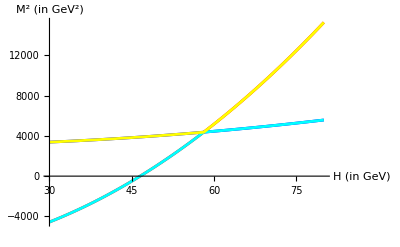

```mathematica
Show[%450,AxesLabel->{HoldForm[HoldForm[H] (in GeV)],HoldForm[HoldForm[M^2] (in GeV^2)]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]}]
```

```mathematica
Export["G:\\My Drive\\Documenten\\natomap\\Master Project\\Images\\Kink.png",%451,"PNG"]
```

G:\My Drive\Documenten\natomap\Master Project\Images\Kink.png

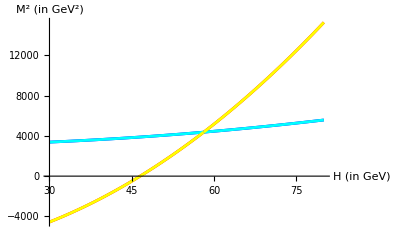

```mathematica
Show[%360,AxesLabel->{HoldForm[HoldForm[H] (in GeV)],HoldForm[HoldForm[M^2] (in GeV^2)]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]}]
```

```mathematica
Export["G:\\My Drive\\Documenten\\natomap\\Master Project\\Images\\Eigenvalues_Sign.png",%361,"PNG"]
```

G:\My Drive\Documenten\natomap\Master Project\Images\Eigenvalues_Sign.png

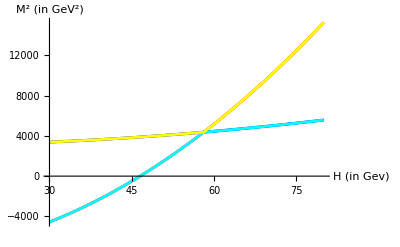

```mathematica
Show[%270,AxesLabel->{HoldForm[HoldForm[H] (in Gev)],HoldForm[HoldForm[M^2] (in GeV^2)]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]}]
```

```mathematica
Export["G:\\My Drive\\Documenten\\natomap\\Master Project\\Images\\Eigenvalues_Sign.png",%271,"PNG"]
```

G:\My Drive\Documenten\natomap\Master Project\Images\Eigenvalues_Sign.png

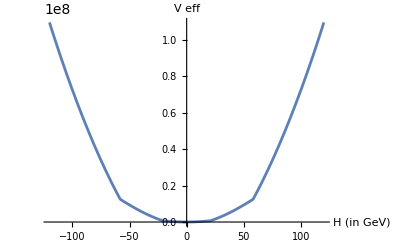

```mathematica
Show[%179,AxesLabel->{HoldForm[H (in GeV)],HoldForm[V eff]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]}]
```

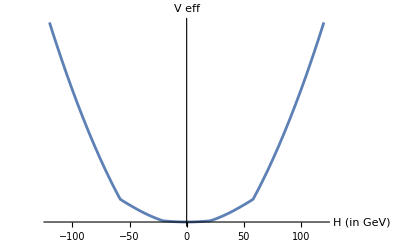

```mathematica
Show[%180,Ticks->{Automatic,None},Method->{"DefaultBoundaryStyle"->Automatic,"DefaultGraphicsInteraction"->{"Version"->1.2,"TrackMousePosition"->{True,False},"Effects"->{"Highlight"->{"ratio"->2},"HighlightPoint"->{"ratio"->2},"Droplines"->{"freeformCursorMode"->True,"placement"->{"x"->"All","y"->"None"}}}},"DefaultMeshStyle"->AbsolutePointSize[6],"ScalingFunctions"->None,"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}}]
```

```mathematica
Export["G:\\My Drive\\Documenten\\natomap\\Master Project\\Images\\BM2_T69_4.png",%181,"PNG"]
```

G:\My Drive\Documenten\natomap\Master Project\Images\BM2_T69_4.png

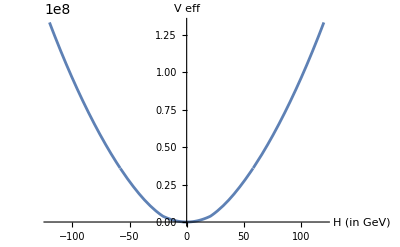

```mathematica
Show[%88,AxesLabel->{HoldForm[H (in GeV)],HoldForm[V eff]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]}]
```

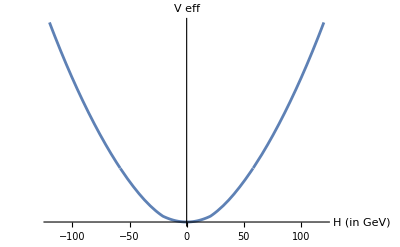

```mathematica
Show[%89,Ticks->{Automatic,None},Method->{"DefaultBoundaryStyle"->Automatic,"DefaultGraphicsInteraction"->{"Version"->1.2,"TrackMousePosition"->{True,False},"Effects"->{"Highlight"->{"ratio"->2},"HighlightPoint"->{"ratio"->2},"Droplines"->{"freeformCursorMode"->True,"placement"->{"x"->"All","y"->"None"}}}},"DefaultMeshStyle"->AbsolutePointSize[6],"ScalingFunctions"->None,"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}}]
```

```mathematica
Export["G:\\My Drive\\Documenten\\natomap\\Master Project\\Images\\BM2_T69_4_sign.png",%90,"PNG"]
```

G:\My Drive\Documenten\natomap\Master Project\Images\BM2_T69_4_sign.png

```mathematica
Show[%1850,AxesLabel->{HoldForm[H (in GeV)],HoldForm[V eff]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]}]
```

-Graphics-

```mathematica
Show[%1851,Ticks->{Automatic,None},Method->{"DefaultBoundaryStyle"->Automatic,"DefaultGraphicsInteraction"->{"Version"->1.2,"TrackMousePosition"->{True,False},"Effects"->{"Highlight"->{"ratio"->2},"HighlightPoint"->{"ratio"->2},"Droplines"->{"freeformCursorMode"->True,"placement"->{"x"->"All","y"->"None"}}}},"DefaultMeshStyle"->AbsolutePointSize[6],"ScalingFunctions"->None,"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}}]
```

-Graphics-

```mathematica
Show[%1144,AxesLabel->{HoldForm[HoldForm[H] (in GeV)],HoldForm[HoldForm[M^2] (in GeV^2)]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

-Graphics-

```mathematica
Export["G:\\My Drive\\Documenten\\natomap\\Master Project\\Images\\Eigenvalues_Sign.png",%1145,"PNG"]
```

G:\My Drive\Documenten\natomap\Master Project\Images\Eigenvalues_Sign.png

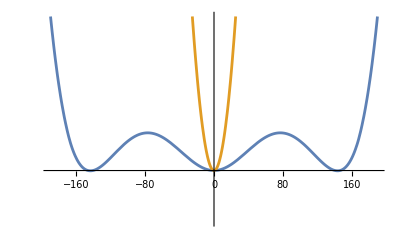

```mathematica
Show[%707,Ticks->{Automatic,None},Method->{"DefaultBoundaryStyle"->Automatic,"DefaultGraphicsInteraction"->{"Version"->1.2,"TrackMousePosition"->{True,False},"Effects"->{"Highlight"->{"ratio"->2},"HighlightPoint"->{"ratio"->2},"Droplines"->{"freeformCursorMode"->True,"placement"->{"x"->"All","y"->"None"}}}},"DefaultMeshStyle"->AbsolutePointSize[6],"ScalingFunctions"->None,"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}}]
```

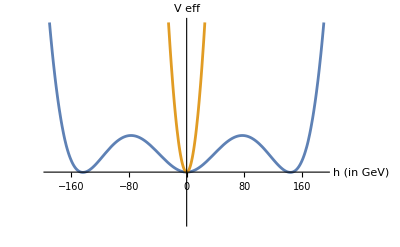

```mathematica
Show[%708,AxesLabel->{HoldForm[h (in GeV)],HoldForm[V eff]},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

```mathematica
Export["G:\\My Drive\\Documenten\\natomap\\Master Project\\Images\\BM1_T117_12_T125.png",%709,"PNG"]
```

G:\My Drive\Documenten\natomap\Master Project\Images\BM1_T117_12_T125.png

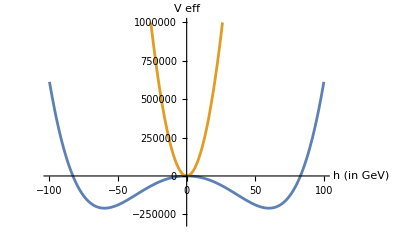

```mathematica
Show[%88,AxesLabel->{HoldForm[h (in GeV)],HoldForm[V eff]},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

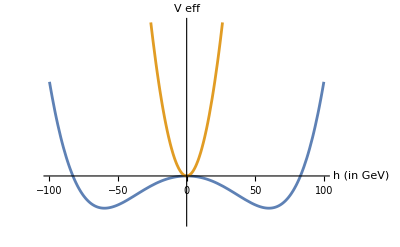

```mathematica
Show[%89,Ticks->{Automatic,None},Method->{"DefaultBoundaryStyle"->Automatic,"DefaultGraphicsInteraction"->{"Version"->1.2,"TrackMousePosition"->{True,False},"Effects"->{"Highlight"->{"ratio"->2},"HighlightPoint"->{"ratio"->2},"Droplines"->{"freeformCursorMode"->True,"placement"->{"x"->"All","y"->"None"}}}},"DefaultMeshStyle"->AbsolutePointSize[6],"ScalingFunctions"->None,"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}}]
```

```mathematica
Export["G:\\My Drive\\Documenten\\natomap\\Master Project\\Images\\Second-order.png",%90,"PNG"]
```

G:\My Drive\Documenten\natomap\Master Project\Images\Second-order.png

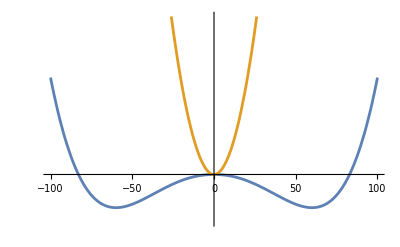

```mathematica
Show[%1147,Ticks->{Automatic,None},AxesStyle->Directive[GrayLevel[0],AbsoluteThickness[1.0150000000000001]],Method->{"DefaultBoundaryStyle"->Automatic,"DefaultGraphicsInteraction"->{"Version"->1.2,"TrackMousePosition"->{True,False},"Effects"->{"Highlight"->{"ratio"->2},"HighlightPoint"->{"ratio"->2},"Droplines"->{"freeformCursorMode"->True,"placement"->{"x"->"All","y"->"None"}}}},"DefaultMeshStyle"->AbsolutePointSize[6],"ScalingFunctions"->None,"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}}]
```

```mathematica
Show[%1148,AxesLabel->{HoldForm[h (in GeV)],HoldForm[V eff]},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

-Graphics-

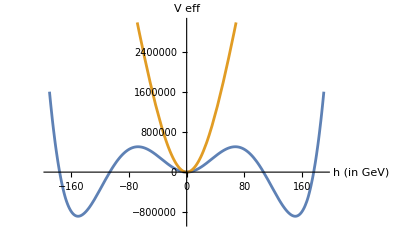

```mathematica
Show[%88,AxesLabel->{HoldForm[h (in GeV)],HoldForm[V eff]},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

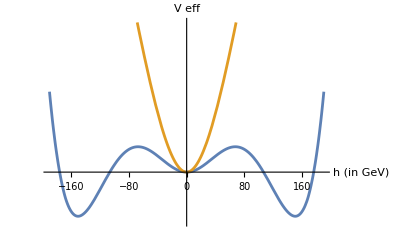

```mathematica
Show[%89,Ticks->{Automatic,None},Method->{"DefaultBoundaryStyle"->Automatic,"DefaultGraphicsInteraction"->{"Version"->1.2,"TrackMousePosition"->{True,False},"Effects"->{"Highlight"->{"ratio"->2},"HighlightPoint"->{"ratio"->2},"Droplines"->{"freeformCursorMode"->True,"placement"->{"x"->"All","y"->"None"}}}},"DefaultMeshStyle"->AbsolutePointSize[6],"ScalingFunctions"->None,"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}}]
```

```mathematica
Export["G:\\My Drive\\Documenten\\natomap\\Master Project\\Images\\BM1_T116_9_T125.png",%90,"PNG"]
```

G:\My Drive\Documenten\natomap\Master Project\Images\BM1_T116_9_T125.png

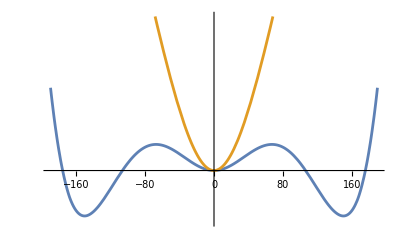

```mathematica
Show[%2126,Ticks->{Automatic,None},Method->{"DefaultBoundaryStyle"->Automatic,"DefaultGraphicsInteraction"->{"Version"->1.2,"TrackMousePosition"->{True,False},"Effects"->{"Highlight"->{"ratio"->2},"HighlightPoint"->{"ratio"->2},"Droplines"->{"freeformCursorMode"->True,"placement"->{"x"->"All","y"->"None"}}}},"DefaultMeshStyle"->AbsolutePointSize[6],"ScalingFunctions"->None,"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}}]
```

```mathematica
Show[%2127,AxesLabel->{HoldForm[h (in GeV)],HoldForm[V eff]},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

-Graphics-

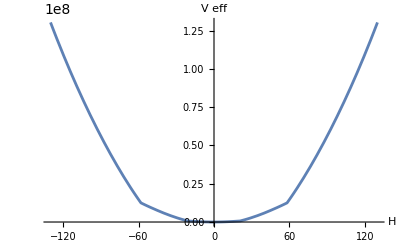

```mathematica
Show[%1679,AxesLabel->{HoldForm[H],HoldForm[V eff]},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

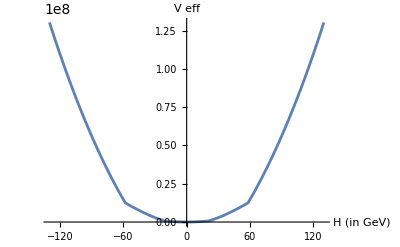

```mathematica
Show[%1680,AxesLabel->{HoldForm[HoldForm[H] (in GeV)],HoldForm[V eff]},PlotLabel->None]
```

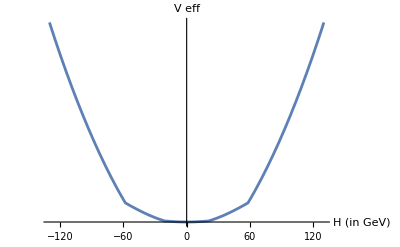

```mathematica
Show[%1772,Ticks->{Automatic,None},Method->{"DefaultBoundaryStyle"->Automatic,"DefaultGraphicsInteraction"->{"Version"->1.2,"TrackMousePosition"->{True,False},"Effects"->{"Highlight"->{"ratio"->2},"HighlightPoint"->{"ratio"->2},"Droplines"->{"freeformCursorMode"->True,"placement"->{"x"->"All","y"->"None"}}}},"DefaultMeshStyle"->AbsolutePointSize[6],"ScalingFunctions"->None,"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}}]
```

```mathematica
Export["G:\\My Drive\\Documenten\\natomap\\Master Project\\Images\\BM2_T69_4.png",%1773,"PNG"]
```

G:\My Drive\Documenten\natomap\Master Project\Images\BM2_T69_4.png

```mathematica
Show[%1680,AxesLabel->{HoldForm[HoldForm[H] (in GeV)],HoldForm[V eff]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

-Graphics-

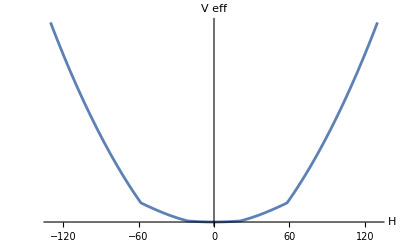

```mathematica
Show[%1680,Ticks->{Automatic,None},Method->{"DefaultBoundaryStyle"->Automatic,"DefaultGraphicsInteraction"->{"Version"->1.2,"TrackMousePosition"->{True,False},"Effects"->{"Highlight"->{"ratio"->2},"HighlightPoint"->{"ratio"->2},"Droplines"->{"freeformCursorMode"->True,"placement"->{"x"->"All","y"->"None"}}}},"DefaultMeshStyle"->AbsolutePointSize[6],"ScalingFunctions"->None,"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}}]
```

```mathematica
Export["G:\\My Drive\\Documenten\\natomap\\Master Project\\Images\\BM2_T69_4.png",%1681,"PNG"]
```

G:\My Drive\Documenten\natomap\Master Project\Images\BM2_T69_4.png

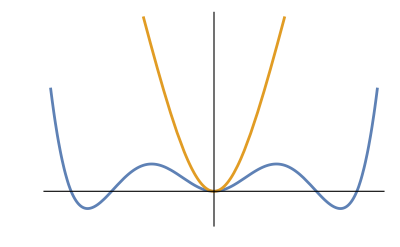

```mathematica
Show[%88,Ticks->None,Method->{"DefaultBoundaryStyle"->Automatic,"DefaultGraphicsInteraction"->{"Version"->1.2,"TrackMousePosition"->{True,False},"Effects"->{"Highlight"->{"ratio"->2},"HighlightPoint"->{"ratio"->2},"Droplines"->{"freeformCursorMode"->True,"placement"->{"x"->"All","y"->"None"}}}},"DefaultMeshStyle"->AbsolutePointSize[6],"ScalingFunctions"->None,"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}}]
```

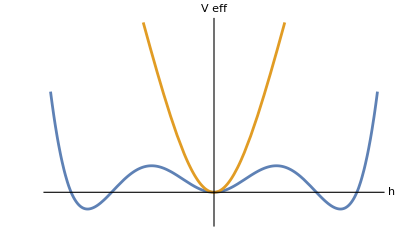

```mathematica
Show[%89,AxesLabel->{HoldForm[h],HoldForm[V eff]},PlotLabel->None,LabelStyle->{16,GrayLevel[0]}]
```

```mathematica
Export["G:\\My Drive\\Documenten\\natomap\\Master Project\\Images\\Effective_potential_1.png",%90,"PNG"]
```

G:\My Drive\Documenten\natomap\Master Project\Images\Effective_potential_1.png

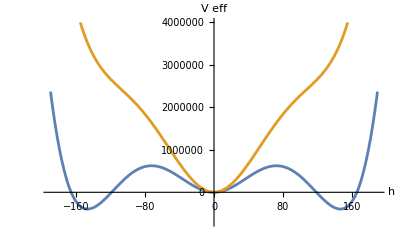

```mathematica
Show[%882,AxesLabel->{HoldForm[h],HoldForm[V eff]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

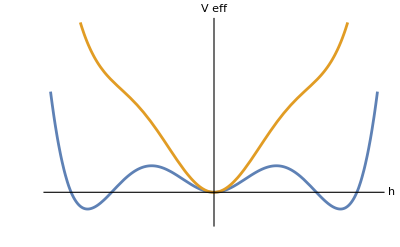

```mathematica
Show[%883,Ticks->None,Method->{"DefaultBoundaryStyle"->Automatic,"DefaultGraphicsInteraction"->{"Version"->1.2,"TrackMousePosition"->{True,False},"Effects"->{"Highlight"->{"ratio"->2},"HighlightPoint"->{"ratio"->2},"Droplines"->{"freeformCursorMode"->True,"placement"->{"x"->"All","y"->"None"}}}},"DefaultMeshStyle"->AbsolutePointSize[6],"ScalingFunctions"->None,"CoordinatesToolOptions"->{"DisplayFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&),"CopiedValueFunction"->({(Identity[#1]&)[#1⟦1⟧],(Identity[#1]&)[#1⟦2⟧]}&)}}]
```

```mathematica
Show[%884,PlotLabel->None,LabelStyle->{15.,GrayLevel[0]}]
```

-Graphics-

```mathematica
Export["G:\\My Drive\\Documenten\\natomap\\Master Project\\Images\\Effective_potential.png",%884,"PNG"]
```

G:\My Drive\Documenten\natomap\Master Project\Images\Effective_potential.png

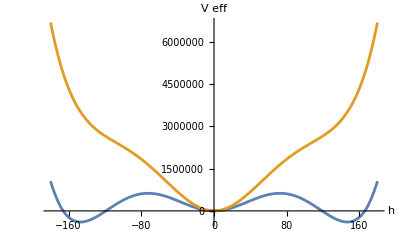

```mathematica
Show[%793,AxesLabel->{HoldForm[h],HoldForm[V eff]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

```mathematica
SystemOpen["eigenvalues.gif"]
```

```mathematica
SystemOpen["anim.gif"]
```

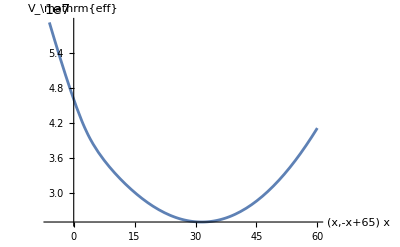

```mathematica
Show[%9823,AxesLabel->{RawBoxes[RowBox[{RowBox[{"(",RowBox[{"x",",",RowBox[{RowBox[{"-","x"}],"+","65"}]}],")"}]," ","x"}]],RawBoxes[RowBox[{RowBox[{"V_","\\","mathrm"}],RowBox[{"{","eff","}"}]}]]},PlotLabel->None,LabelStyle->{GrayLevel[0]}]
```

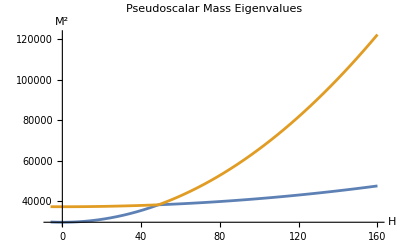

120

```mathematica
Show[%4323,PlotLabel->HoldForm[Pseudoscalar Mass Eigenvalues],LabelStyle->{GrayLevel[0]}]
```